```mathematica
$Assumptions={n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals}
```

{n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals}

```mathematica
Integrate[(ⅇ^(-(-d+x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2))) ⅇ^(ⅈ (p-p0) x),{x,-∞,∞}]
```

```mathematica
ⅇ^(-(p-p0)^2 σ^2) (ⅇ^(-ⅈ d (p-p0))+ⅇ^(-ⅈ d (p-p0))ⅇ^(2 ⅈ d (p-p0)))
```

```mathematica
ⅇ^(-(p-p0)^2 σ^2) (Cos[d (p-p0)])
```

ⅇ^(-(p-p0)^2 σ^2) Cos[d (p-p0)]

```mathematica
Integrate[ⅇ^(-(p-p0)^2 σ^2) Cos[d (p-p0)] ⅇ^(ⅈ (-a p^2 t+p x)),{p,-∞,∞}]
```

1/(2 √(ⅈ a t+σ^2))ⅇ^(-(d^2-2 d x+x^2+4 ⅈ d p0 σ^2+4 ⅈ a p0^2 t σ^2-4 ⅈ p0 x σ^2)/(4 (ⅈ a t+σ^2))) √π ((1+ⅇ^((d (ⅈ x+2 p0 σ^2))/(a t-ⅈ σ^2))) Cos[d p0]-ⅈ (-1+ⅇ^((d (ⅈ x+2 p0 σ^2))/(a t-ⅈ σ^2))) Sin[d p0])

```mathematica
S0f[x_,y_,d_,σ_]:= (ⅇ^(-y^2/(4 σ^2)) (ⅇ^(-(-d+x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2))))/(2 √π √((1+ⅇ^(-d^2/(2 σ^2))) σ^2))
```

```mathematica
Integrate[S0f[x,y,d,σ] S0f[x,y,d,σ],{x,-∞,∞},{y,-∞,∞}]
```

1

```mathematica
Integrate[S0f[x,y,d,σ] ⅇ^(ⅈ px x+ⅈ py y),{x,-∞,∞},{y,-∞,∞}]
```

```mathematica
(2 ⅇ^(-(px^2+py^2) σ^2) (ⅇ^(-ⅈ d px)+ⅇ^(-ⅈ d px)ⅇ^(2 ⅈ d px)) √π σ)/(√(1+ⅇ^(-d^2/(2 σ^2))))
```

```mathematica
(2 ⅇ^((-px^2-py^2) σ^2) (2 Cos[d px]) √π σ)/(√(1+ⅇ^(-d^2/(2 σ^2))))
```

(4 ⅇ^((-px^2-py^2) σ^2) √π σ Cos[d px])/(√(1+ⅇ^(-d^2/(2 σ^2))))

```mathematica
ⅇ^(ⅈ( px x+py y - a t(px^2 + py^2)))
```

ⅇ^(ⅈ (-a (px^2+py^2) t+px x+py y))

```mathematica
Integrate[ⅇ^((-px^2-py^2) σ^2) Cos[d px] ⅇ^(ⅈ (-a (px^2+py^2) t+px x+py y)),{px,-∞,∞},{py,-∞,∞}]
```

(ⅇ^(-y^2/(4 (ⅈ a t+σ^2))) (ⅇ^(-(d-x)^2/(4 (ⅈ a t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ a t+σ^2)))) π)/(2 (ⅈ a t+σ^2))

```mathematica
FullSimplify[ⅇ^(-y^2/(4 (ⅈ a t+σ^2)))ⅇ^(-y^2/(4 (-ⅈ a t+σ^2)))]
```

ⅇ^(-(y^2 σ^2)/(2 (a^2 t^2+σ^4)))

```mathematica
St=((2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4))/σ)^(-1/2)(ⅇ^(-(d-x)^2/(4 (ⅈ a t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ a t+σ^2))))
```

```mathematica
Stc=((2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4))/σ)^(-1/2)(ⅇ^(-(d-x)^2/(4 (-ⅈ a t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ a t+σ^2))))
```

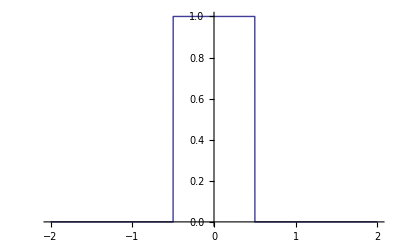

```mathematica
Plot[UnitBox[x/1], {x, -2,2}]
```

```mathematica
Integrate[UnitBox[x/d]ⅇ^(ⅈ k x), {x, -∞, ∞}]
```

Piecewise[{{-(2 Sin[(d k)/2])/k, d<0}, {(2 Sin[(d k)/2])/k, d>0}, {0, True}}]